## Start

```mathematica
Clear["`*"]
e=1.6*10^-19;kB=1.38*10^-23;dens=10^19;temp=10^3*e/kB;pres0=kB dens*temp;μ0=1.25663706212*10^-6;
shotno=3;
shot={"77651","54719","68408"};
folder=NotebookDirectory[];
folderdata=FileNameJoin[{folder,shot⟦shotno⟧}];
If[!DirectoryQ[folderdata],CreateDirectory[folderdata,CreateIntermediateDirectories->True]];
SetDirectory[folderdata];
files=FileNames["*.dat"]⟦1;;1⟧;
data4=Table[Flatten[Import[files⟦i⟧]],{i,Length[files]}];
(*assesing information from imported data*)
np=129;{RDIM,ZDIM,RCENTR,RLEFT,ZMID,RMAXIS,ZMAXIS,SIMAG,SIBRY,BCENTR,CURRENT,psi0,a1,a2,a3,a4,a5,a6,a7,a8}=Transpose[data4⟦All,1;;20⟧];
factorscal=1;
{SIMAG,SIBRY}=factorscal{SIMAG,SIBRY};
```

## Build quantities: grid and on-the-grid

```mathematica
(*R-Z grid*)
δR=Table[RDIM⟦i⟧-0RLEFT[[i]],{i,Length[data4]}]/(np-1);δZ=Table[ZDIM⟦i⟧,{i,Length[data4]}]/(np-1);R=Table[Table[RLEFT⟦i⟧+δR⟦i⟧ (Range[np]-1),{j,np}]//Transpose,{i,Length[data4]}];
Z=Table[Table[ZMID[[i]]+(2 Range[np]-np-1)/2 δZ⟦i⟧,{j,np}],{i,Length[data4]}];
(*F,P,F',P'*)
FPOL=data4⟦All,20+0 np+1;;20+1 np⟧;
PRES=data4⟦All,20+1 np+1;;20+2 np⟧;
FFPRIM=factorscal data4⟦All,20+2 np+1;;20+3 np⟧;
PPRIME=factorscal data4⟦All,20+3 np+1;;20+4 np⟧;
(*q,ψ,∂_R ψ,∂_Z ψ,∂_RR ψ,∂_RZ ψ,∂_ZZ ψ*)
Q=data4⟦All,20+(np+4) np+1;;20+(np+5) np⟧;
PSI=Table[ArrayReshape[data4⟦i,20+4 np+1;;20+(np+4) np⟧,{np,np}]//Transpose,{i,Length[data4]}];
PSIR=Table[(RotateLeft[PSI⟦i⟧,{1,0}]-RotateLeft[PSI⟦i⟧,{-1,0}])/(2δR[[i]]),{i,Length[data4]}];
PSIZ=Table[(RotateLeft[PSI⟦i⟧,{0,1}]-RotateLeft[PSI⟦i⟧,{0,-1}])/(2δZ[[i]]),{i,Length[data4]}];
(*PSIRR=Table[(RotateLeft[PSIR⟦i⟧,{1,0}]-RotateLeft[PSIR⟦i⟧,{-1,0}])/(2δR[[i]]),{i,Length[data4]}];
PSIRZ=Table[(RotateLeft[PSIR⟦i⟧,{0,1}]-RotateLeft[PSIR⟦i⟧,{0,-1}])/(2δZ[[i]]),{i,Length[data4]}];
PSIZZ=Table[(RotateLeft[PSIZ⟦i⟧,{0,1}]-RotateLeft[PSIZ⟦i⟧,{0,-1}])/(2δZ[[i]]),{i,Length[data4]}];*)

PSIRR=Table[(RotateLeft[PSI[[i]],{1,0}]-2 PSI[[i]]+RotateLeft[PSI[[i]],{-1,0}])/δR[[i]]^2,{i,Length[data4]}];

PSIRZ=Table[(RotateLeft[PSI[[i]],{1,1}]-RotateLeft[PSI[[i]],{1,-1}]-RotateLeft[PSI[[i]],{-1,1}]+RotateLeft[PSI[[i]],{-1,-1}])/(4 δR[[i]] δZ[[i]]),{i,Length[data4]}];

PSIZZ=Table[(RotateLeft[PSI[[i]],{0,1}]-2 PSI[[i]]+RotateLeft[PSI[[i]],{0,-1}])/δZ[[i]]^2,{i,Length[data4]}];

(*plasma boundary*)
{nbbbs,limitr}=data4[[All,20+(np+5)np+1;;20+(np+5)np+2]]//Transpose;
rbound=Table[data4[[as,23+(np+5)np;;22+(np+5)np+2nbbbs[[as]]]],{as,Length[data4]}];
zbound=Table[rbound[[as,2i]],{as,Length[data4]},{i,nbbbs[[as]]}];
rbound=Table[rbound[[as,2i-1]],{as,Length[data4]},{i,nbbbs[[as]]}];
(*not for tcv!!!
rlim=Table[data4[[as,23+(np+5)np+2nbbbs[[as]];;22+(np+5)np+2nbbbs[[as]]+2limitr[[as]]]],{as,Length[data4]}];
zlim=Table[rlim[[as,2i]],{as,Length[data4]},{i,limitr[[as]]}];
rlim=Table[rlim[[as,2i-1]],{as,Length[data4]},{i,limitr[[as]]}];*)
(*magnetic axis position and field*)
R0=RMAXIS;
B0=FPOL[[All,1]]/RMAXIS;
(*Evaluating F(ψ) on the R-Z grid*)
ℱ=Φt=ρ=Range[Length[data4]];
ρ2=Range[Length[data4]];
Monitor[For[as=1,as≤Length[data4],as++,npp=np;Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);F=Interpolation[Transpose[{ψ,FPOL⟦as⟧}]];ℱ⟦as⟧=F[PSI⟦as⟧];(*Φt[[as]]=Table[Total[ℱ⟦as⟧/R[[as]] HeavisideTheta[Max[ψ⟦j⟧,SIMAG[[as]]]-PSI⟦as⟧]HeavisideTheta[-Min[ψ⟦j⟧,SIMAG[[as]]]+PSI⟦as⟧] δR⟦as⟧ δZ⟦as⟧,2],{j,Length[ψ]}];
Φt⟦as⟧=Φt⟦as⟧/Φt⟦as,Length[ψ]⟧//Sqrt;
Fρ=Interpolation[Transpose[{ψ,Φt⟦as⟧}]];
ρ⟦as⟧=Fρ[PSI⟦as⟧];
*)
Φt[[as]]=Prepend[Accumulate[1/2 (Most[Q⟦as⟧]+Rest[Q⟦as⟧]) Differences[ψ]],0.];Φt⟦as⟧=√(Φt[[as]]/Last[Φt[[as]]]);Fρ=Interpolation[Transpose[{ψ,Φt⟦as⟧}]];ρ⟦as⟧=Fρ[PSI⟦as⟧];

];,{as}]


ρR=Table[(RotateLeft[ρ⟦i⟧,{1,0}]-RotateLeft[ρ⟦i⟧,{-1,0}])/(2δR[[i]]),{i,Length[data4]}];
ρZ=Table[(RotateLeft[ρ⟦i⟧,{0,1}]-RotateLeft[ρ⟦i⟧,{0,-1}])/(2δZ[[i]]),{i,Length[data4]}];

(*Evaluating Subscript[q, θ](ψ,θ) on the R-Z grid*)
qθ=-Table[(((R⟦as⟧-RMAXIS⟦as⟧)^2+(Z⟦as⟧-ZMAXIS[[as]])^2) ℱ⟦as⟧)/(R⟦as⟧ (Z⟦as⟧-ZMAXIS[[as]]) PSIZ⟦as⟧+R⟦as⟧ (R⟦as⟧-RMAXIS⟦as⟧) PSIR⟦as⟧),{as,Length[data4]}];

(*Estimate triangulation, geoemtrical center, *){Rmax,Rmin,Zmax,Rsup}=Table[{Max[rbound⟦as⟧],Min[rbound⟦as⟧],Max[zbound⟦as⟧],rbound⟦as,1⟧},{as,Length[data4]}]//Transpose;
{a,Rgeo}={(Rmax-Rmin)/2,(Rmax+Rmin)/2};
{δ,κ}={(Rgeo-Rsup)/a,(2Zmax)/a/2};
raza=Table[√((R⟦as⟧-R0⟦as⟧)^2+Z⟦as⟧^2)+0.00,{as,Length[R]}];
```

InterpolatingFunction::dmval: Input value {0.00661798} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00643146} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00625367} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

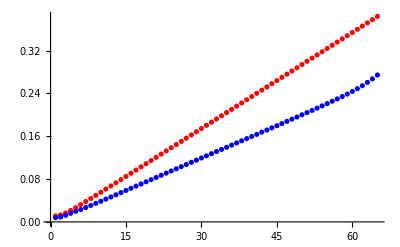
{-Graphics-,-Graphics3D-}

```mathematica
{ListPlot[{raza⟦1,65,65;;129⟧,a⟦1⟧ ρ⟦1,65,65;;129⟧},PlotStyle->{Red,Blue}],
ListPlot3D[{raza⟦1⟧/a⟦1⟧,ρ⟦1⟧},PlotRange->{{30,100},{30,100},{0,1}},PlotStyle->{Red,Blue}]}
```

```mathematica
as=1;boundary=Transpose[{rbound⟦as⟧,zbound⟦as⟧}];
boundaryPolygon=Polygon[boundary];insideQ=RegionMember[boundaryPolygon];
points=Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[ρ⟦as⟧]}];
filteredPoints=Select[points,insideQ[{#1⟦1⟧,#1⟦2⟧}]&];
points=Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[raza⟦as⟧/a[[as]]]}];
filteredPoints2=Select[points,insideQ[{#1⟦1⟧,#1⟦2⟧}]&];
ListPlot3D[{filteredPoints,filteredPoints2},PlotRange->All]
```

-Graphics3D-

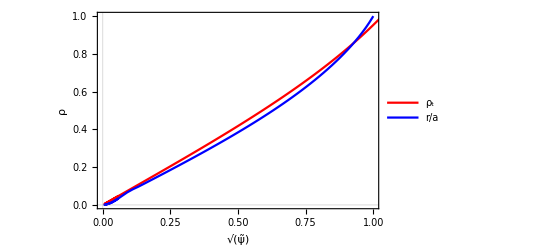

```mathematica
ListLinePlot[{Transpose[{((PSI⟦1,65;;np,65⟧-SIMAG⟦1⟧)/(SIBRY⟦1⟧-SIMAG⟦1⟧))//Sqrt,raza⟦1,65;;np,65⟧/a⟦1⟧}],Transpose[{((PSI⟦1,65;;np,65⟧-SIMAG⟦1⟧)/(SIBRY⟦1⟧-SIMAG⟦1⟧))//Sqrt, ρ⟦1,65;;np,65⟧}]},PlotStyle->{Red,Blue},PlotRange->{{0,1},{0,1}},PlotTheme->"Scientific",LabelStyle->{Black,Bold,15},FrameLabel->{"√(ψ̃)","ρ"},PlotLegends->Placed[{"ρ_t","r/a"},{0.8,0.2}]]
```

```mathematica
(*Proof that RMAXIS is the real magnetic axis where ∇ψ=0*)
```

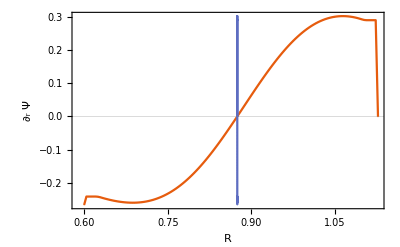
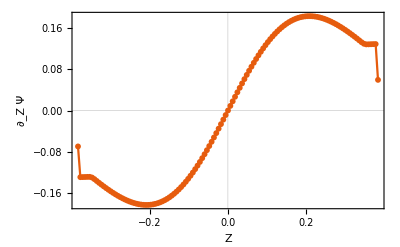

```mathematica
as=1;fas=(np-1)/2;
{ListLinePlot[{Transpose[{R⟦as,All,fas⟧,PSIR⟦as,All,fas⟧}],Transpose[{R⟦as,All,fas⟧ 0+RMAXIS⟦as⟧,PSIR⟦as,All,fas⟧}]},PlotMarkers->{Automatic,1},PlotTheme->"Scientific",FrameLabel->{"R","∂_r Ψ"},LabelStyle->{Black,Bold,10}],ListLinePlot[Transpose[{Z⟦as,fas⟧,PSIZ⟦as,fas⟧}],PlotMarkers->{Automatic,6},PlotTheme->"Scientific",FrameLabel->{"Z","∂_Z Ψ"},LabelStyle->{Black,Bold,10}]}
```

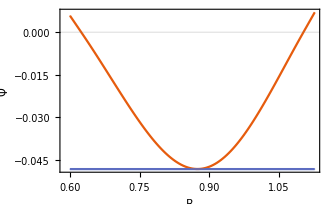
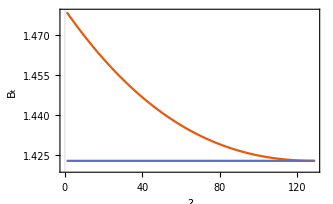

```mathematica
(*Proof that SIMAG is the poloidal flux at the magnetic axis*){ListLinePlot[{Transpose[{R⟦as,All,fas⟧,PSI⟦as,All,fas⟧}],Transpose[{R⟦as,All,fas⟧,SIMAG[[as]]+0PSI⟦as,All,fas⟧}]},PlotMarkers->{Automatic,1},PlotTheme->"Scientific",FrameLabel->{"R","Ψ"},LabelStyle->{Black,Bold,15},ImageSize->333],ListLinePlot[{FPOL[[as]]/RCENTR[[as]],BCENTR[[as]]+FPOL[[as]]0},PlotMarkers->{Automatic,1},PlotTheme->"Scientific",FrameLabel->{"?","B_t"},LabelStyle->{Black,Bold,15},ImageSize->333]}
```

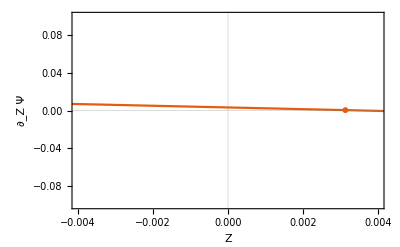

```mathematica
ListLinePlot[Transpose[{Z⟦as,fas⟧,PSIZ⟦as,fas⟧}],PlotRange->{.2{-0.02,0.02},{-0.1,0.1}},PlotMarkers->{Automatic,6},PlotTheme->"Scientific",FrameLabel->{"Z","∂_Z Ψ"},LabelStyle->{Black,Bold,10}]
```

```mathematica
(*Checking the poloidal flux grid*)
```

InterpolatingFunction::dmval: Input value {0.00661798} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00643146} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00625367} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

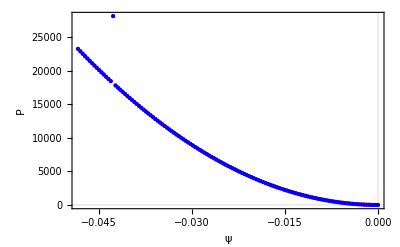
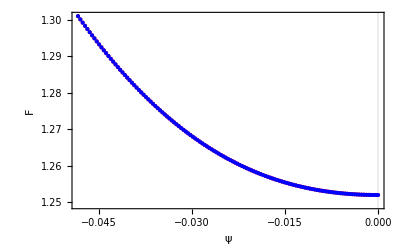
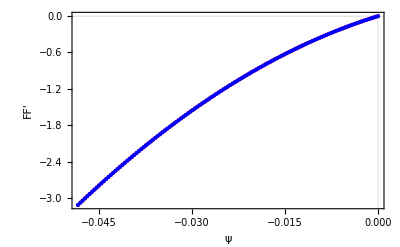
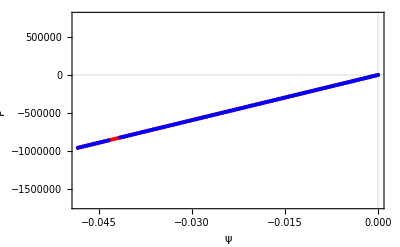
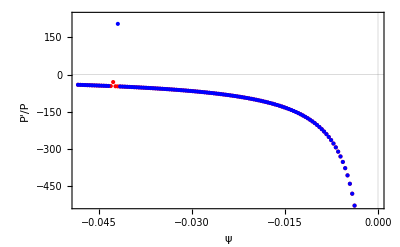

-Graphics3D-

```mathematica
as=1;npp=np;Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);
{q,P,F,pp,ffp}={Interpolation[Transpose[{ψ,Q⟦as⟧}]],Interpolation[Transpose[{ψ,PRES⟦as⟧}]],Interpolation[Transpose[{ψ,FPOL⟦as⟧}]],Interpolation[Transpose[{ψ,PPRIME⟦as⟧}]],Interpolation[Transpose[{ψ,FFPRIM⟦as⟧}]]};
{PP[x_],FF[x_],PPRZ,FFPRZ}={D[P[x], x],F[x] D[F[x], x],pp[PSI⟦as⟧],ffp[PSI⟦as⟧]};
{lhs,rhs,psin}={GaussianFilter[PSIRR⟦as⟧-PSIR⟦as⟧/R⟦as⟧+PSIZZ⟦as⟧,4],-μ0 R⟦as⟧^2 PPRZ-FFPRZ,(PSI⟦as⟧-SIMAG⟦as⟧)/(SIBRY⟦as⟧-SIMAG⟦as⟧)};
pts=Flatten[Table[{R⟦as,i,j⟧,Z⟦as,i,j⟧,lhs⟦i,j⟧,rhs⟦i,j⟧,psin⟦i,j⟧},{i,2,np-1},{j,2,np-1}],1];
pts=Select[pts,0.02<#1⟦5⟧<0.98&];
range=Max[Abs[Flatten[pts⟦All,{3,4}⟧]]];
grafix[a_,b_,c_,d_]:=ListPlot[{Transpose[{ψ,a}],Transpose[{ψ,b}]},PlotTheme->"Scientific",FrameLabel->{c,d},PlotStyle->{Red,Blue},LabelStyle->{Black,Bold,10}];
{grafix[PRES⟦as⟧,P[ψ],"ψ","P"],grafix[FPOL⟦as⟧,F[ψ],"ψ","F"],grafix[FFPRIM⟦as⟧,FF[ψ],"ψ","FF'"],grafix[PPRIME⟦as⟧,PP[ψ],"ψ","P'"],grafix[PPRIME⟦as⟧/PRES[[as]],PP[ψ]/P[ψ],"ψ","P'/P"]}
p1=ListPlot3D[{pts⟦All,{1,2,3}⟧,pts⟦All,{1,2,4}⟧},PlotRange->{All,All,{Min[pts⟦All,3⟧],Max[pts⟦All,3⟧]}},PlotStyle->{Red,Blue},PlotLegends->{"lhs","rhs"},AxesLabel->{"R","Z"},PlotLabel->"GradShafranov"]
```

```mathematica
(*Toroidal current*)
```

```mathematica
𝒥=Range[Length[R]];Monitor[For[as=1,as≤Length[R],as++,npp=np;Δ=(SIBRY⟦as⟧-SIMAG⟦as⟧)/(npp-1);ψ=SIMAG⟦as⟧+Δ (Range[npp]-1);{q,P,F}={Interpolation[Transpose[{ψ,Q⟦as⟧}]],Interpolation[Transpose[{ψ,PRES⟦as⟧}]],Interpolation[Transpose[{ψ,FPOL⟦as⟧}]]};{PP[x_],FF[x_]}={D[P[x], x],F[x] D[F[x], x]};𝒥⟦as⟧=(R⟦as⟧ PP[PSI⟦as⟧]+FF[PSI⟦as⟧]/(μ0 R⟦as⟧));],as]
```

InterpolatingFunction::dmval: Input value {0.00661798} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00643146} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00625367} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
Table[(2 Max[Z⟦as⟧] (Max[R⟦as⟧]-Min[R⟦as⟧]))/Length[R⟦as⟧]^2 Total[HeavisideTheta[SIBRY⟦as⟧-PSI⟦as⟧] 𝒥⟦as⟧,2],{as,Length[R]}]/CURRENT
```

{-0.997529}

```mathematica
as=1;ListPlot3D[HeavisideTheta[SIBRY[[as]]-PSI[[as]]]𝒥⟦as⟧/10^5,PlotRange->{All,All,All}]
```

-Graphics3D-

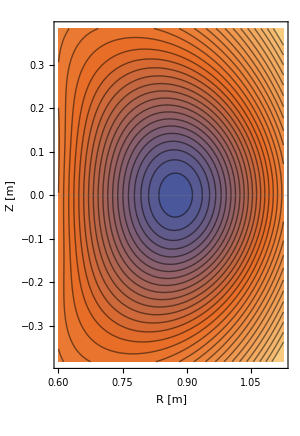
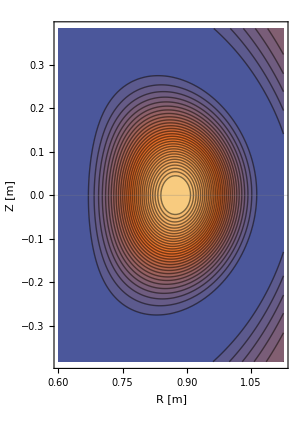

```mathematica
(*Plasma Boundary, tokamak volume, poloidal flux and F in contourplots*)as=1;grafs={ListContourPlot[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[PSI⟦as⟧]}],Contours->30,AspectRatio->{Max[R⟦as⟧],2 Max[Z⟦as⟧]},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]","ψ"},LabelStyle->{Black,Bold,15},ImageSize->300],ListContourPlot[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[ℱ⟦as⟧]}],Contours->30,AspectRatio->{Max[R⟦as⟧],2 Max[Z⟦as⟧]},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]","F[ψ]"},LabelStyle->{Black,Bold,15},ImageSize->300]}
```

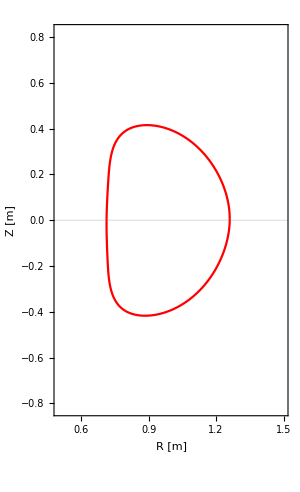

```mathematica
ListLinePlot[Transpose[{rbound⟦as⟧,zbound⟦as⟧}/R0⟦as⟧],PlotRange->{{0.5,1.5},{-(3 a⟦as⟧)/R0⟦as⟧,(3 a⟦as⟧)/R0⟦as⟧}},AspectRatio->{1.5 R0⟦as⟧,6 a⟦as⟧},PlotStyle->{Red},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]"},LabelStyle->{Black,Bold,15},ImageSize->300]
```

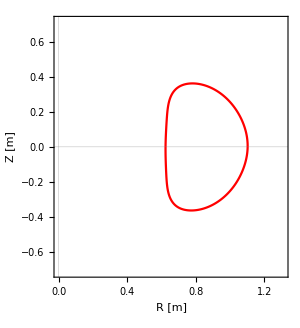
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Plasma Boundary, tokamak volume, poloidal flux and F in contourplots*)as=1;grafs={ListLinePlot[Transpose[{rbound⟦as⟧,zbound⟦as⟧}],PlotRange->{{0,1.5 R0[[as]]},{-3a[[as]],3a[[as]]}},AspectRatio->{1.5R0[[as]],6a[[as]]},PlotStyle->{Red},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]"},LabelStyle->{Black,Bold,15},ImageSize->300],ListContourPlot[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[PSI⟦as⟧]}],Contours->30,AspectRatio->{Max[R⟦as⟧],2 Max[Z⟦as⟧]},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]","ψ"},LabelStyle->{Black,Bold,15},ImageSize->300],ListContourPlot[Transpose[{Flatten[R⟦as⟧],Flatten[Z⟦as⟧],Flatten[ℱ⟦as⟧]}],Contours->30,AspectRatio->{Max[R⟦as⟧],2 Max[Z⟦as⟧]},PlotTheme->"Scientific",FrameLabel->{"R [m]","Z [m]","F[ψ]"},LabelStyle->{Black,Bold,15},ImageSize->300]}
```

## Exporting real

```mathematica
(* ============================================================ *)
(* SETTINGS                                                     *)
(* ============================================================ *)
radius = 4;

order = 4;          (* smoothed psi + 1D MHD profiles *)
orderRaw = 3;       (* raw psi used as flux label and for chi *)
ngrid = 200;
nSurf = 30;
nChi = 256;
smin = 0.01;
smax = 0.995;
orderChi = 3;
orderChiDer = 2;
(* ============================================================ *)
(* derivative with respect to flux-surface label s              *)
(* ============================================================ *)

Clear[dSurf];
dSurf[arr_,h_]:=Module[{d},d=ConstantArray[0.,Dimensions[arr]];
  (* centered differences *)
 d⟦2;;-2⟧=(arr⟦3;;All⟧-arr⟦1;;-3⟧)/(2 h);
  (* second-order one-sided differences *)
d[[1]]=(-3arr[[1]]+4arr[[2]]-arr[[3]])/(2h);
d[[-1]]=(3arr[[-1]]-4arr[[-2]]+arr[[-3]])/(2h);d];
(* Optional: launch parallel kernels once *)
LaunchKernels[];

(* ============================================================ *)
(* MAIN EQUILIBRIUM LOOP                                        *)
(* ============================================================ *)
Monitor[For[as=1,as<=Length[R],as++,
(* 1. GEOMETRY AND OUTPUT GRID                                *)
{minR,maxR,minZ,maxZ}={Min[rbound⟦as⟧],Max[rbound⟦as⟧],Min[zbound⟦as⟧],Max[zbound⟦as⟧]};
rgrid=R⟦as,All,1⟧;
zgrid=Z⟦as,1,All⟧;
rnew=Subdivide[minR,maxR,ngrid-1];
znew=Subdivide[minZ,maxZ,ngrid-1];
ℛ=Outer[#1&,rnew,znew];
𝒵=Outer[#2&,rnew,znew];
  (* ========================================================== *)
  (* 2. PSI INTERPOLANTS                                        *)
  (*                                                            *)
  (* CapitalPsi     : smoothed psi, used for exported            *)
  (*                  psi and derivatives                        *)
  (*                                                            *)
  (* CapitalPsiRaw  : original psi, used for flux labels         *)
  (*                  and straight-field-line coordinate         *)
  (* ========================================================== *)

Ψ=ListInterpolation[GaussianFilter[PSI⟦as⟧,radius],{rgrid,zgrid},InterpolationOrder->order];
Ψraw=ListInterpolation[PSI⟦as⟧,{rgrid,zgrid},InterpolationOrder->orderRaw];
ΨrawR=Derivative[1,0][Ψraw];
ΨrawZ=Derivative[0,1][Ψraw];
  (* ========================================================== *)
  (* 3. EXPORTED PSI AND DERIVATIVES                            *)
  (* ========================================================== *)

ψ0=Ψ[ℛ,𝒵];
ψprof=Ψraw[ℛ,𝒵];
ψr=Derivative[1,0][Ψ][ℛ,𝒵];
ψz=Derivative[0,1][Ψ][ℛ,𝒵];
ψrr=Derivative[2,0][Ψ][ℛ,𝒵];
ψrz=Derivative[1,1][Ψ][ℛ,𝒵];
ψzz=Derivative[0,2][Ψ][ℛ,𝒵];
  (* ========================================================== *)
  (* 4. RHO AND DERIVATIVES                                    *)
  (* ========================================================== *)

Ρ=ListInterpolation[ρ⟦as⟧,{rgrid,zgrid},InterpolationOrder->order];
ρint=Ρ[ℛ,𝒵];
ρintR=Derivative[1,0][Ρ][ℛ,𝒵];
ρintZ=Derivative[0,1][Ρ][ℛ,𝒵];
 (* 5. 1-D EQUILIBRIUM PROFILES                               *)
  ψ=Subdivide[SIMAG⟦as⟧,SIBRY⟦as⟧,np-1];
fF=Interpolation[Transpose[{ψ,FPOL⟦as⟧}],InterpolationOrder->order];
ℱs=fF[ψprof];
 (* dF/dpsi = FF'/F *)
fFprim=Interpolation[Transpose[{ψ,FFPRIM⟦as⟧/FPOL⟦as⟧}],InterpolationOrder->order];
Fψprim=fFprim[ψprof];(* q(psi) *)
fq=Interpolation[Transpose[{ψ,Q⟦as⟧}],InterpolationOrder->order];
qψ=fq[ψprof]; (* ========================================================== *)
  (* 6. qprim = dq/drho                                        *)
  (*                                                            *)
  (* CapitalPhi_t is rho at this stage of your code             *)
  (* ========================================================== *)

fρψ=Interpolation[Transpose[{ψ,Φt⟦as⟧}],InterpolationOrder->order];
fqSmooth=Interpolation[Transpose[{ψ,GaussianFilter[Q⟦as⟧,radius]}],InterpolationOrder->order];
qprim=fqSmooth'[ψprof]/fρψ'[ψprof];(* ========================================================== *)
  (*                                                          *)
  (*       STRAIGHT-FIELD-LINE ANGLE CHI                       *)
  (*                                                          *)
  (* ========================================================== *)


  (* ========================================================== *)
  (* 7. SURFACE LABELS AND CHI GRID                             *)
  (* ========================================================== *)

Rout=Max[rbound⟦as⟧];
surf=Subdivide[smin,smax,nSurf-1];
ds=surf⟦2⟧-surf⟦1⟧;(* Do not duplicate chi=0 with chi=2 Pi *)

χgrid=(2 π Range[0,nChi-1])/nChi;
  (* ========================================================== *)
  (* 8. TRACE FLUX SURFACES USING CHI AS INDEPENDENT VARIABLE  *)
  (*                                                            *)
  (* dR/dchi =  q R/F psi_Z                                    *)
  (* dZ/dchi = -q R/F psi_R                                    *)
  (* ========================================================== *)

curves=With[{psiIF=Ψraw,psiRIF=ΨrawR,psiZIF=ΨrawZ,fFchi=fF,fqchi=fq,Raxis=RMAXIS⟦as⟧,Zaxis=ZMAXIS⟦as⟧,Rout0=Rout,surf0=surf,chiGrid0=χgrid},ParallelTable[Module[{r00,z00,ψsurf,qsurf,Fsurf,rr,zz,u,sol,rcurve,zcurve},r00=Raxis+surf0⟦j⟧ (Rout0-Raxis);z00=Zaxis;ψsurf=psiIF[r00,z00];qsurf=fqchi[ψsurf];Fsurf=fFchi[ψsurf];sol=NDSolveValue[{rr'[u]==-((qsurf rr[u]) psiZIF[rr[u],zz[u]])/Fsurf,zz'[u]==((qsurf rr[u]) psiRIF[rr[u],zz[u]])/Fsurf,rr[0]==r00,zz[0]==z00},{rr,zz},{u,0,2 π}];rcurve=sol⟦1⟧/@chiGrid0;zcurve=sol⟦2⟧/@chiGrid0;{rcurve,zcurve,qsurf,Fsurf}],{j,nSurf}]];
  (* 9. STRUCTURED MAP (s,chi) -> (R,Z)                        *)
Rtab=curves⟦All,1⟧;
Ztab=curves⟦All,2⟧;
qsurfTab=curves⟦All,3⟧;
FsurfTab=curves⟦All,4⟧; 
 (* 10. DERIVATIVES ACROSS FLUX SURFACES                      *)
  RsTab=dSurf[Rtab,ds];
ZsTab=dSurf[Ztab,ds];
  (* 11. DERIVATIVES ALONG CHI                                 *)
  (*                                                            *)
  (* Taken directly from the trajectory equations rather       *)
  (* than by numerical differentiation                         *)
  ψRtab=ΨrawR[Rtab,Ztab];
ψZtab=ΨrawZ[Rtab,Ztab];
qOverF=qsurfTab/FsurfTab;
qOverFtab=Outer[Times,qOverF,ConstantArray[1.,nChi]];
RχTab=-qOverFtab Rtab ψZtab;
ZχTab=qOverFtab Rtab ψRtab;
(* 12. INVERSE JACOBIAN                                      *)
  (*                                                            *)
  (* J = R_s Z_chi - R_chi Z_s                                 *)
  (*                                                            *)
  (* chi_R = -Z_s/J                                            *)
  (* chi_Z =  R_s/J                                            *)
  Jac=RsTab ZχTab-RχTab ZsTab;
χRtab=-ZsTab/Jac;
χZtab=RsTab/Jac;
  (* 13. SCATTERED R-Z DATA                                    *)
 rrData=Flatten[Rtab];
zzData=Flatten[Ztab];
χData=Flatten[ConstantArray[χgrid,nSurf]];
χRData=Flatten[χRtab];
χZData=Flatten[χZtab];
coords=Transpose[{rrData,zzData}];
dataSin=MapThread[{#1,#2}&,{coords,Sin[χData]}];
dataCos=MapThread[{#1,#2}&,{coords,Cos[χData]}];
dataChiR=MapThread[{#1,#2}&,{coords,χRData}];
dataChiZ=MapThread[{#1,#2}&,{coords,χZData}];

  (* 14. INTERPOLANTS FOR CHI, CHI_R, CHI_Z                    *)
  Sχ=Interpolation[dataSin,InterpolationOrder->orderChi];
Cχ=Interpolation[dataCos,InterpolationOrder->orderChi];
χRinterp=Interpolation[dataChiR,InterpolationOrder->orderChiDer];
χZinterp=Interpolation[dataChiZ,InterpolationOrder->orderChiDer];

  (* 15. RANGE IN WHICH CHI WAS ACTUALLY CONSTRUCTED           *)
ψout=ψprof;
ψinner=Ψraw[RMAXIS⟦as⟧+smin (Rout-RMAXIS⟦as⟧),ZMAXIS⟦as⟧];
ψouter=Ψraw[RMAXIS⟦as⟧+smax (Rout-RMAXIS⟦as⟧),ZMAXIS⟦as⟧];
{ψmin,ψmax}=MinMax[{ψinner,ψouter}];
mask=Map[ψmin≤#1≤ψmax&,ψout,{2}];
  (* 16. EVALUATE CHI ON THE SAME R-Z GRID AS ALL MHD DATA     *)
Sout=Sχ[ℛ,𝒵];
Cout=Cχ[ℛ,𝒵];
χraw=Mod[ArcTan[Cout,Sout],2 π];
χRraw=χRinterp[ℛ,𝒵];
χZraw=χZinterp[ℛ,𝒵];
(* Use numeric filler outside the region where chi exists.   *)
  (* Do NOT export Indeterminate into QQ.                       *)
  (* ---------------------------------------------------------- *)

χ0=MapThread[If[#1,#2,0.]&,{mask,χraw},2];
χintR=MapThread[If[#1,#2,0.]&,{mask,χRraw},2];
χintZ=MapThread[If[#1,#2,0.]&,{mask,χZraw},2];
  (* ========================================================== *)
  (* 17. ALL EXPORTED QUANTITIES                               *)
  (* ========================================================== *)

MHD={Flatten[ψ0],Flatten[ψr],Flatten[ψz],Flatten[ψrr],Flatten[ψrz],Flatten[ψzz],Flatten[ℱs],Flatten[Fψprim],Flatten[qψ],Flatten[qprim],Flatten[ρint],Flatten[ρintR],Flatten[ρintZ],Flatten[χ0],Flatten[χintR],Flatten[χintZ]};
Nqua=Length[MHD];
  (* ========================================================== *)
  (* 18. HEADER + EXPORT                                       *)
  (* ========================================================== *)

QQ=Flatten[{R0[[as]],B0[[as]],ngrid,ngrid,minR,maxR,minZ,maxZ,a[[as]],δ[[as]],κ[[as]],Nqua,MHD}];
Export[FileNameJoin[{folderdata,"QQ_"<>StringTake[files[[as]],-7]}],QQ];
],as
]
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

InterpolatingFunction::dmval: Input value {0.00435081} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00421525} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.00408298} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

General::stop: Further output of Interpolation::udeg will be suppressed during this calculation.

InterpolatingFunction::femdmval: Input value {0.62403,-0.364852} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.62403,-0.361195} lies outside the range of data in the interpolating function.

InterpolatingFunction::femdmval: Input value {0.62403,-0.357538} lies outside the range of data in the interpolating function.

General::stop: Further output of InterpolatingFunction::femdmval will be suppressed during this calculation.

```mathematica
curve=Transpose[{rbound⟦as-1⟧/R0[[as-1]],zbound⟦as-1⟧/R0[[as-1]],1+0zbound[[as-1]]}];Show[ListPlot3D[{ℛ/R0[[as-1]]//Flatten,𝒵/R0[[as-1]]//Flatten,ρint//Flatten}//Transpose,PlotRange->{All,All,{-1,1}},Mesh->None,ColorFunction->"TemperatureMap"],Graphics3D[{Thick,Red,Line[curve]}],AxesLabel->{"x","y","z"}]
```

-Graphics3D-